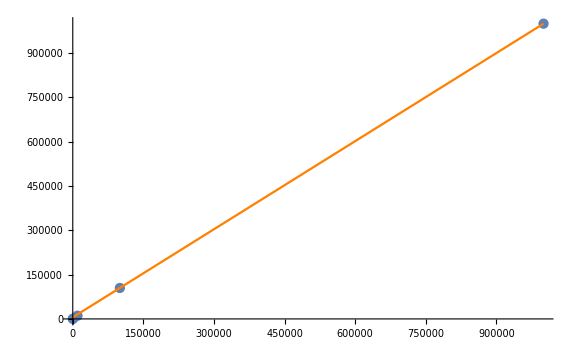

| Estimate | Standard Error | t-Statistic | P-Value
1 | 5424.55 | 311.045 | 17.4398 | 0.000410896
x | 0.994396 | 0.000326228 | 3048.16 | 7.78678×10^-11

1.

```mathematica
(* Importiere Daten*)
Ohm100 =Import["/Users/chegerland/Desktop/Praktikum_QL/Messung/100ohm.dat","FieldSeparators"->","];
Ohm1k =Import["/Users/chegerland/Desktop/Praktikum_QL/Messung/1000ohm.dat","FieldSeparators"->","];
Ohm10k =Import["/Users/chegerland/Desktop/Praktikum_QL/Messung/10kOhm.dat","FieldSeparators"->","];
Ohm100k =Import["/Users/chegerland/Desktop/Praktikum_QL/Messung/100kOhm.dat","FieldSeparators"->","];
Ohm1M =Import["/Users/chegerland/Desktop/Praktikum_QL/Messung/1MOhm.dat","FieldSeparators"->","];

(* Berechne Mittel der Widerstände *)
a =Sum[1/Sqrt[Ohm100[[n,1]]^2+Ohm100[[n,2]]^2],{n,Length[Ohm100]}]/Length[Ohm100];
b =Sum[1/Sqrt[Ohm1k[[n,1]]^2+Ohm1k[[n,2]]^2],{n,Length[Ohm1k]}]/Length[Ohm1k];
c =Sum[1/Sqrt[Ohm10k[[n,1]]^2+Ohm10k[[n,2]]^2],{n,Length[Ohm10k]}]/Length[Ohm10k];
d =Sum[1/Sqrt[Ohm100k[[n,1]]^2+Ohm100k[[n,2]]^2],{n,Length[Ohm100k]}]/Length[Ohm100k];
e =Sum[1/Sqrt[Ohm1M[[n,1]]^2+Ohm1M[[n,2]]^2],{n,Length[Ohm1M]}]/Length[Ohm1M];

(* linearer Fit mit Auswertung*)
data = {{100,a},{1000,b},{10000,c},{100000,d},{1000000,e}};
errors = {0.1,1,10,1000,10000};
lm = LinearModelFit[data,x,x,Weights->errors];
Show[ListPlot[data,PlotRange->Full],Plot[lm[x],{x,0,1000000},PlotStyle->Orange],ImageSize->Large]
lm["ParameterTable"]
lm["AdjustedRSquared"]
```

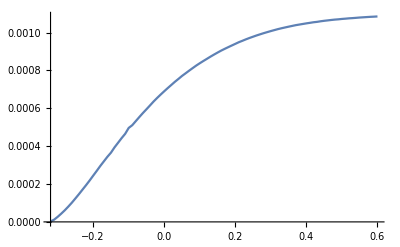

```mathematica
(* Importiere Struktur G*)
G = Import["/Users/chegerland/Desktop/Praktikum_QL/Messung/G.dat","FieldSeparators"->","];

(* Lege Arrays für Spannungen und Leitwerte an *)
Spannungen = {};
Do[Spannungen=Append[Spannungen,G[[n,1]]],{n,Length[G]}];
Leitwerte = {};
Do[Leitwerte=Append[Leitwerte,Sqrt[G[[n,2]]^2 + G[[n,3]]^2  ]],{n,Length[G]}]
data2 = Transpose[{Spannungen,Leitwerte}];

(* Plot *)
ListPlot[data2,Joined->True, AxesOrigin->{Min[Spannungen],0}]
```

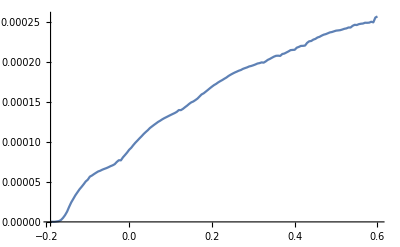

```mathematica
(* Importiere Struktur I*)
J= Import["/Users/chegerland/Desktop/Praktikum_QL/Messung/QL_I.dat","FieldSeparators"->","];

(* Lege Arrays für Spannungen und Leitwerte an *)
Spannungen = {};
Do[Spannungen=Append[Spannungen,J[[n,1]]],{n,Length[J]}];
Leitwerte = {};
Do[Leitwerte=Append[Leitwerte,Sqrt[J[[n,2]]^2 + J[[n,3]]^2  ]],{n,Length[J]}]
data2 = Transpose[{Spannungen,Leitwerte}];

(* Plot *)
ListPlot[data2,Joined->True, AxesOrigin->{Min[Spannungen],0}]
```

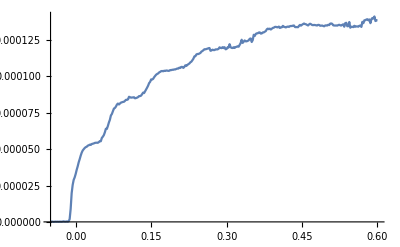

```mathematica
(* Importiere Struktur L*)
L = Import["/Users/chegerland/Desktop/Praktikum_QL/Messung/L.dat","FieldSeparators"->","];

(* Lege Arrays für Spannungen und Leitwerte an *)
Spannungen = {};
Do[Spannungen=Append[Spannungen,L[[n,1]]],{n,Length[L]}];
Leitwerte = {};
Do[Leitwerte=Append[Leitwerte,Sqrt[L[[n,2]]^2 + L[[n,3]]^2  ]],{n,Length[L]}]
data2 = Transpose[{Spannungen,Leitwerte}];

(* Plot *)
ListPlot[data2,Joined->True, AxesOrigin->{Min[Spannungen],0}]
```

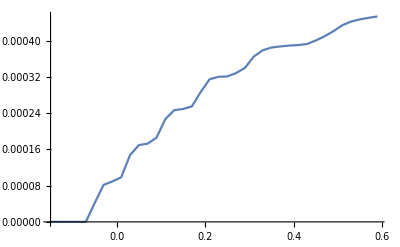

```mathematica
(* Importiere Struktur L_fein*)
Lfein= Import["/Users/chegerland/Desktop/Praktikum_QL/Messung/Lfein.dat","FieldSeparators"->","];

(* Lege Arrays für Spannungen und Leitwerte an *)
Spannungen = {};
Do[Spannungen=Append[Spannungen,Lfein[[n,1]]],{n,Length[Lfein]}];
Leitwerte = {};
Do[Leitwerte=Append[Leitwerte,Sqrt[Lfein[[n,2]]^2 + Lfein[[n,3]]^2  ]],{n,Length[Lfein]}]
data2 = Transpose[{Spannungen,Leitwerte}];

(* Plot *)
ListPlot[data2,Joined->True, AxesOrigin->{Min[Spannungen],0}]
```